```mathematica
AppendDelta[p_,q_,current_,distance_]:= Module[{digits,foundOld, foundNew,posOld, posNew,next, treshHold},
digits= IntegerDigits[current,p];
treshHold=Quotient[p-1,2];
foundOld=0;
For[posOld=1,posOld≤ Length[digits], posOld++,
If[digits[[posOld]]> treshHold,
foundOld=posOld; 
Break[]]
];
digits= IntegerDigits[current+distance,p];
foundNew=0;
For[posNew=1,posNew≤ Length[digits], posNew++,
If[digits[[posNew]]> treshHold, 
foundNew=posNew; 
Break[]]
];
Return [foundOld-foundNew]
]
```

```mathematica
FirstNonGood[p_,current_]:= Module[{digits,found, pos, treshHold},
digits= IntegerDigits[current,p];
treshHold=Quotient[p-1,2];
found=0;
For[pos=1,pos≤ Length[digits], pos++,
If[digits[[pos]]> treshHold,
found=Length[digits]-pos+1; 
Break[]]
];
found= found/Length[digits];
Return [found]
]
```

```mathematica
Clear[CalcDeltas]
```

```mathematica
Doebie[tuple_, start_,stopAt_] := Module[{current,lowest,logCurrent, index, dummy, range=1000, continue, distance,l=Length[tuple],zero=0,primeIndex=1, attempt=1, result={}},
index = 0;
current = start;
lowest = Infinity;
result={};

(* now calculate good values and append them to the file for as long as the bound is not reached *)
(* If the process is aborted, the file is closed *)

CheckAbort[
Monitor[
While[Length[result]<stopAt,
distance = Distance[current, tuple[[primeIndex]]];
logCurrent=N[Log[10,distance]];
If[logCurrent<lowest,lowest=Abs[logCurrent]];
current += distance;
AppendTo[result,FirstNonGood[tuple[[1]],current]];
If [distance == 0,
zero+=1;
(*Print[{current,primeIndex,zero,distance}];*)
If[zero==l,
index +=1;
zero=0;
current+=1,
attempt=0,
lowest = Infinity
],
zero=0
];
attempt+=1;
primeIndex=Mod[primeIndex,l]+1;
]
,
"Calculating good values " <> ToString[tuple] <> ". " <> ToString[index] <> " found."<> "- " <> ToString[N[Log[10,current],50]] <> "  " <> ToString[Length[result]]<> "  " <> ToString[logCurrent]<> "  (" <> ToString[lowest] <> ")"
];
,
Print["Aborted at value : " <> ToString[current] ];
];
Return[result]
]
```

```mathematica
vals=CalcDeltas[{3,5,7,11},10^850000,100]
```

{1676722/1676723,-838357/838362,-1/838362,-1/838362,279453/279454,-1,0,0,1,-1676721/1676725,4/1676725,-8/1676725,1,-838362/838363,0,1/1676726,1676723/1676726,-838361/838363,-3/1676726,0,1676725/1676726,-186302/186303,1/1676727,0,1676717/1676727,-1676716/1676727,-11/1676727,0,1,-1676723/1676728,1/838364,-3/838364,1676727/1676728,-1676725/1676729,-2/1676729,0,1676727/1676729,-1676729/1676730,1676729/2811425169630,0,1676729/1676731,-1676726/1676731,-1/1676731,0,1676727/1676731,-88248/88249,-12/1676731,-1/1676731,1676725/1676731,-1676720/1676731,-3/1676731,0,1676723/1676731,-1676727/1676731,-2/1676731,0,1676729/1676731,-419181/419183,-3/838366,0,838365/838366,-838363/838366,0,-1/838366,419182/419183,-419182/419183,-1/419183,0,1,-1676732/1676733,0,0,1676732/1676733,-1676729/1676734,-5/1676734,0,1,-1676729/1676735,0,0,1676729/1676735,-335346/335347,-1/1676735,-2/1676735,1676733/1676735,-838367/838368,-1/1676736,0,1676735/1676736,-1676734/1676737,9/1676737,-10/1676737,1676735/1676737,-1676722/1676737,1/1676737,-11/1676737,1676732/1676737,-1676729/1676737,-2/1676737,0}

```mathematica
vals=CalcDeltas[{3,5,7,11},10^850000,100]
```

{1,-1781512/1781519,0,-6/1781519,1781518/1781519,-593837/593840,-1/445380,-1/445380,1781519/1781520,-1781520/1781521,0,-1/1781521,1,-890760/890761,0,2/890761,890758/890761,-1781519/1781522,0,0,1781519/1781522,-1781513/1781522,11/1781522,-6/890761,890757/890761,-890754/890761,-7/1781522,-1/890761,1781517/1781522,-890756/890761,-9/1781522,-1/1781522,1,-593840/593841,2/1781523,-5/1781523,1,-1781523/1781524,19596763/3173829544100,-7/1781525,356304/356305,-1781522/1781525,0,0,1781522/1781525,-356304/356305,0,-1/1781525,1781521/1781525,-356303/356305,-1/356305,-1/1781525,1781521/1781525,-593839/593842,1/593842,-2/890763,890759/890763,-890755/890763,-5/1781526,0,1781515/1781526,-890759/890763,0,0,890759/890763,-890755/890763,-1/593842,0,1781513/1781526,-890752/890763,-7/1781526,-1/1781526,890756/890763,-890755/890763,-1/1781526,-1/1781526,890756/890763,-1781513/1781526,-1/1781526,-1/890763,890758/890763,-1781507/1781526,-1/296921,4/890763,593835/593842,-593835/593842,-5/1781526,0,890755/890763,-1781507/1781526,-2/890763,0,593837/593842,-890755/890763,-1/1781526,0,593837/593842,-890756/890763,-1/593842,0}

```mathematica
vals=CalcDeltas[{3,5,7},10^1000000,100]
```

{4191806/4191807,-4191803/4191808,1/523976,-1/1047952,4191799/4191808,-4191799/4191808,0,3/4191808,1047949/1047952,-4191789/4191808,-5/4191808,0,2095897/2095904,-4191785/4191808,-1/523976}

```mathematica
vals=CalcDeltas[{3,5,7},10^100000,10000]
```

{209588/209591,-1,1/34932,34931/34932,-104795/104796,-1/209592,209591/209592,-209586/209593,-4/209593,209590/209593,-209583/209593,-2/209593,209585/209593,-209581/209593,-8/209593,209589/209593,-209585/209593,-1/209593,209586/209593,-209585/209593,0,209585/209593,-209580/209593,-6/209593,209586/209593,-209578/209593,-4/209593,209582/209593,-209586/209593,0,209586/209593,-104794/104797,2/104797,104792/104797,-104794/104797,0,104794/104797,-104792/104797,4/104797,104788/104797,-19053/19054,0,19053/19054,-29939/29942,«8672»,-104285/104797,0,104285/104797,-208563/209594,0,208563/209594,-104282/104797,-1/209594,29795/29942,-104283/104797,15/209594,29793/29942,-104281/104797,3/209594,208559/209594,-104275/104797,-5/104797,9480/9527,-208559/209594,-1/209594,9480/9527,-208559/209594,0,208559/209594,-104278/104797,-1/104797,14897/14971,-104278/104797,-1/209594,208557/209594,-104261/104797,-15/209594,29791/29942,-208547/209594,0,208547/209594,-18959/19054,0,18959/19054,-104271/104797,-2/104797,104273/104797,-208543/209594,0}

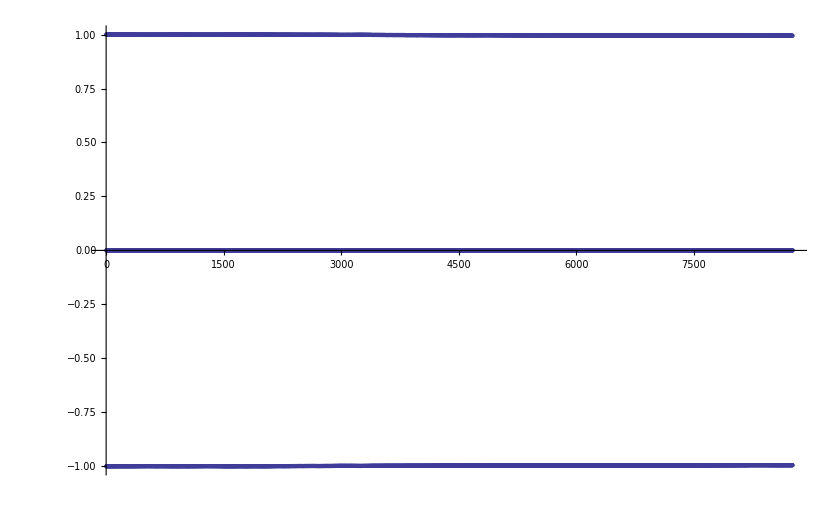

```mathematica
ListPlot[vals, Filling->None]
```

```mathematica
vals=Doebie[{3,31,43,173,229},0,100000]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2,1/2,1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,1/3,1/3,1/3,1/3,0,0,0,0,0,0,0,0,0,0,0,1/3,1/3,1/3,1/3,0,0,1/2,1/2,1/2,0,0,0,1,1,0,1/6,1/3,1/3,1/3,0,0,0,1/2,5/6,0,5/7,1,1,1,0,1/8,1/8,1/2,3/8,0,0,0,0,0,0,0,0,0,0,0,1/8,1/8,1/8,1/8,0,0,0,0,0,0,0,0,0,0,0,1/8,1/8,1/8,1/8,0,0,1/2,1/2,«99762»,277/300,277/300,277/300,277/300,0,91/100,91/100,11/12,277/300,0,137/150,137/150,139/150,47/50,0,137/150,71/75,71/75,71/75,0,11/12,47/50,143/150,19/20,0,287/300,29/30,29/30,73/75,0,293/300,59/60,59/60,59/60,0,137/150,293/300,49/50,99/100,0,298/301,298/301,299/301,299/301,0,292/301,291/301,42/43,295/301,0,291/301,293/301,296/301,296/301,0,297/301,297/301,297/301,297/301,0,291/301,298/301,298/301,298/301,0,291/301,289/301,290/301,42/43,0,296/301,297/301,297/301,297/301,0,299/302,297/302,297/302,1,0,295/303,295/303,296/303,296/303,0,284/303,284/303,295/303,295/303,0,97/101,290/303,289/303,289/303,0,290/303,290/303,290/303,290/303,0,289/303,286/303,286/303,290/303,0,284/303,280/303,97/101,97/101,0,286/303,93/101,97/101,97/101,0,290/303,287/303,96/101,97/101}

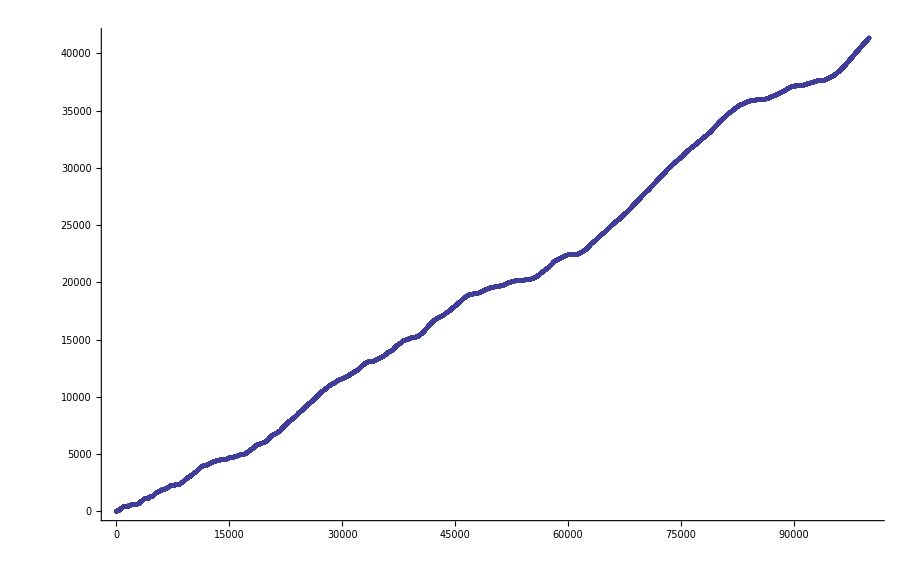

```mathematica
ListPlot[Accumulate[vals],PlotRange->All]
```

```mathematica
vals2=Doebie[{3,37,59,127,139},0,200000]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,4,4,4,0,0,0,3,4,0,2,2,2,2,0,3,3,3,3,0,0,0,4,5,0,6,6,6,6,0,6,6,6,6,0,1,4,5,5,0,0,3,4,4,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,4,5,5,0,7,7,9,9,0,0,5,5,5,0,2,2,2,1,0,0,4,4,4,0,0,0,0,«199662»,130,130,130,130,0,124,127,127,130,0,122,128,128,128,0,127,127,127,127,0,132,132,125,125,0,128,128,129,129,0,122,122,122,122,0,121,121,121,121,0,113,114,114,116,0,111,109,112,112,0,110,110,110,110,0,108,108,108,107,0,96,104,108,102,0,103,101,101,108,0,105,108,108,108,0,104,104,110,110,0,109,109,108,111,0,99,111,111,111,0,103,107,109,113,0,109,112,115,115,0,111,109,109,108,0,114,115,115,115,0,97,101,111,110,0,114,115,115,115,0,104,105,110,105,0,104,102,109,109,0,115,115,115,117,0,116,118,119,119,0,108,111,113,113,0,113,113,115,115,0,100,104,111,107,0,114,114,114,114,0,97,117,117,117,0,108,114,114,114}

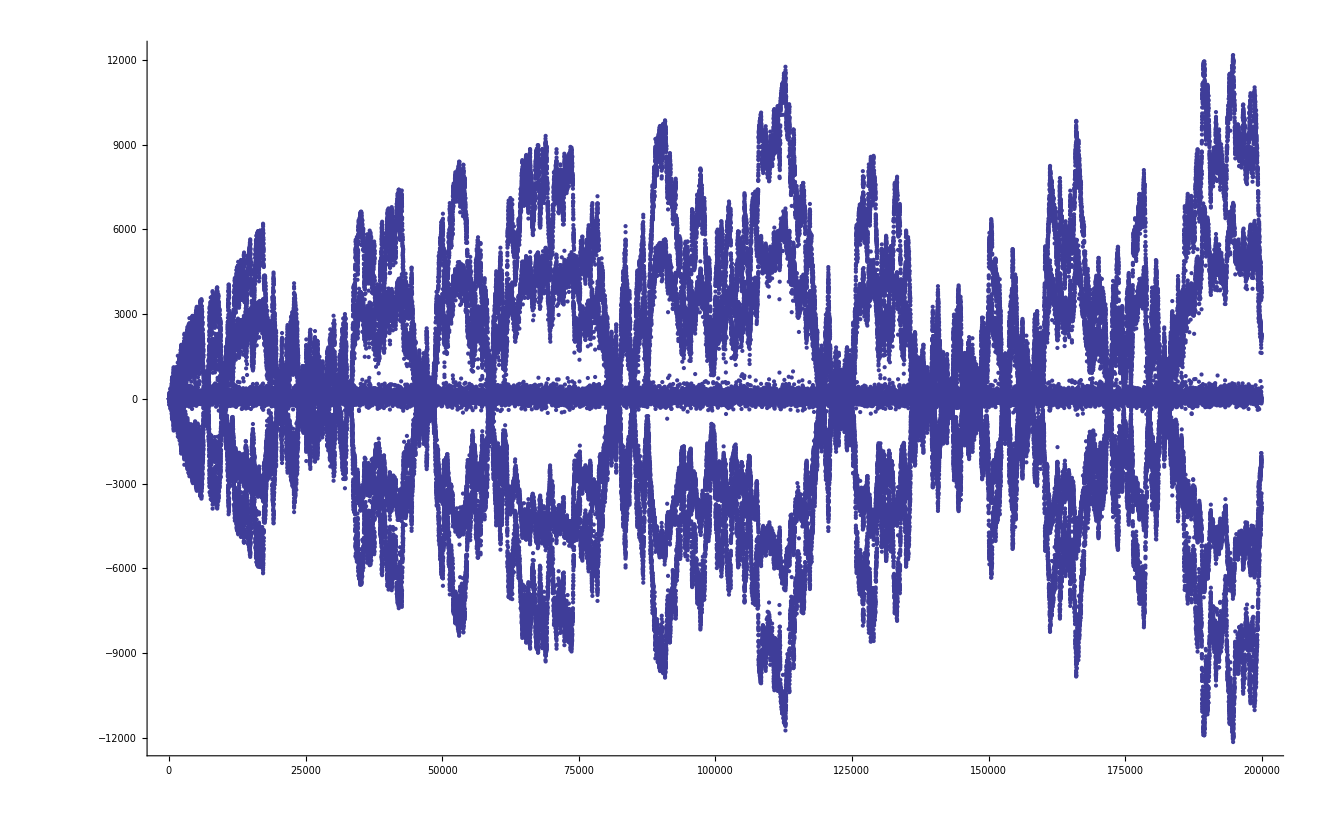

```mathematica
ListPlot[Differences[Differences[Differences[Differences[Differences[Differences[Differences[vals2]]]]]]],PlotRange->All]
```

```mathematica
vals3=Doebie[{3,5},0,100000]
```

{0,0,0,0,0,1,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,2,0,2,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,2,0,6,0,3,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,1,0,4,0,6,0,5,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,1,0,2,0,0,0,0,0,0,0,5,0,1,0,0,0,0,0,2,0,0,0,0,0,1,0,1,0,0,0,0,0,2,0,0,0,0,0,0,0,1,0,9,0,1,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,2,0,1,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,6,0,3,0,0,0,0,0,0,«99528»,0,3,0,0,0,0,0,0,0,0,0,3,0,3,0,6,0,5,0,3,0,0,0,0,0,1,0,2,0,0,0,5,0,4,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,4,0,1,0,0,0,0,0,2,0,0,0,0,0,0,0,1,0,9,0,0,0,0,0,0,0,1,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,1,0,0,0,0,0,3,0,9,0,5,0,0,0,0,0,0,0,2,0,3,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,4,0,2,0,0,0,0,0,1,0,2,0,4,0,4,0,3,0,1,0,0,0,0,0,2,0,0,0,4,0,10,0,6,0,1,0,0,0,0,0,2,0,1,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,7,0,8,0,1,0,0,0,0,0,0,0,4,0,4,0,2}

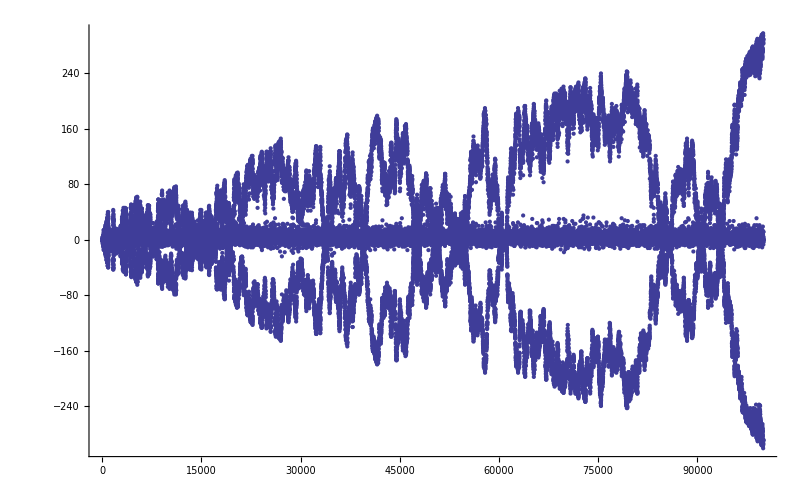

```mathematica
ListPlot[Differences[vals],PlotRange->All]
```

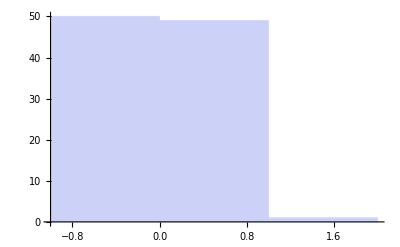

```mathematica
Histogram[vals]
```

```mathematica
N[Sum[i,{i,vals}]]
```

0.999986

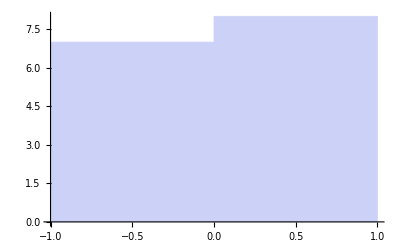

```mathematica
Histogram[vals]
```

```mathematica
N[Skewness[vals]]
```

-0.0184021

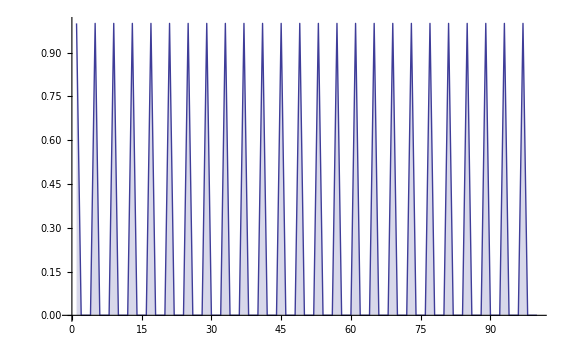

```mathematica
ListLinePlot[Accumulate[vals], Filling->Axis]
```

```mathematica
N[Skewness[vals]]
```

4.07379×10^-6

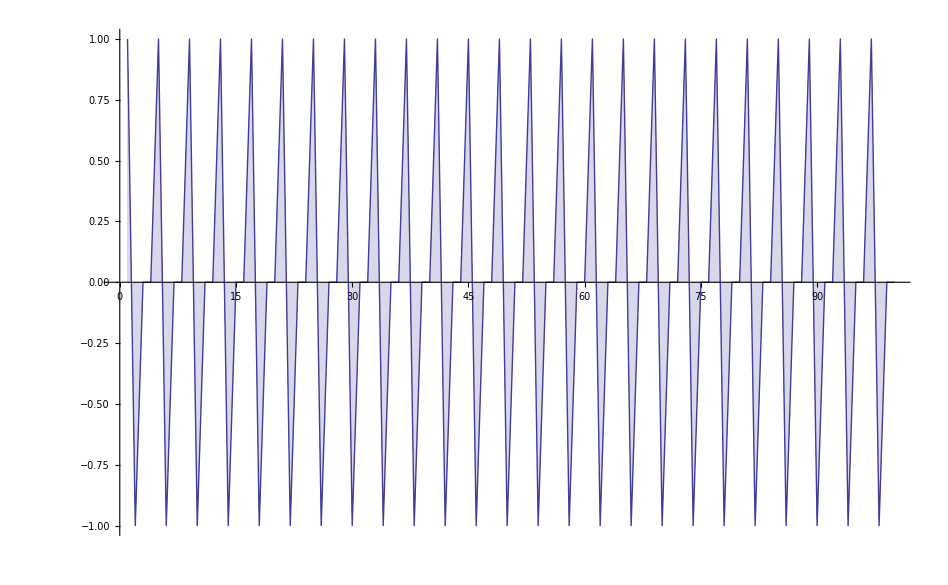

```mathematica
ListLinePlot[vals, Filling->Axis]
```

```mathematica
vals2=CalcDeltas[{5,3},0,10^10000,10000]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2/3,-1/2,0,0,0,0,-1/4,0,0,0,0,-1/4,-2/5,0,0,0,0,-1/5,0,0,0,0,-2/5,-4/5,0,0,0,0,0,0,0,0,0,0,-1/6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/2,0,0,0,0,0,0,0,0,0,0,0,-1/6,0,0,0,-2/3,0,0,0,0,0,0,0,0,-1/7,0,0,0,0,-3/7,0,0,0,0,-1/7,0,0,0,0,0,0,-2/7,-2/7,0,0,-1/7,0,0,0,-1/7,-2/7,0,0,0,0,0,0,0,0,0,0,0,0,0,-2/7,-5/7,-6/7,-3/8,0,0,0,0,0,-1/4,0,0,0,0,0,0,0,0,0,0,0,-1/8,-1/4,0,0,-1/8,0,0,0,0,-1/8,-1/4,0,0,0,0,-1/8,0,0,0,0,-3/8,-1/8,0,0,0,-1/8,0,0,0,0,-1/4,0,0,0,0,0,0,0,«9626»,0,0,0,-1/8,0,0,0,0,-1/4,-1/8,0,0,0,0,0,0,-1/16,-3/8,-1/2,-5/16,-1/8,0,0,0,0,-1/16,-1/8,0,0,-1/16,0,0,0,0,-1/16,0,0,0,0,-3/16,-1/8,0,0,0,-1/16,-1/8,-3/16,0,0,0,0,0,0,0,-1/8,0,0,0,0,-3/16,-1/8,0,0,0,-1/16,0,0,0,0,-1/16,-3/8,-5/16,-3/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,-3/16,-1/16,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/16,0,0,0,0,0,0,-1/16,0,0,0,0,0,0,0,0,0,0,0,-3/16,-5/16,-1/16,-1/16,0,0,0,0,0,-1/16,0,0,0,0,0,0,0,0,0,0,0,-1/16,0,0,0,0,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3/16,-1/4,-3/16,0,0,0,0,-1/16,0,0,0,0,0,-1/8,-3/16,-7/16,-3/16}

```mathematica
vals3=CalcDeltas[{11,7,5,3},10^100000,10^200000,10]
```

{-48012/48013,1/96026,-1/48013,-96023/96026,-3/96026,2/96027,-32007/32009,-2/96027,0,-32008/32009}

```mathematica
Select[vals3,#<-0.5&]
```

{-48012/48013,-96023/96026,-32007/32009,-32008/32009}

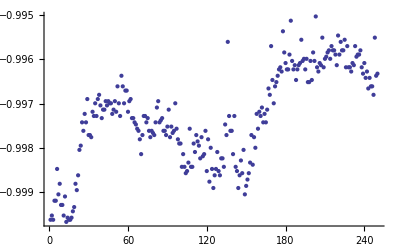

```mathematica
ListPlot[Select[vals,#<-0.5&],PlotRange->All]
```

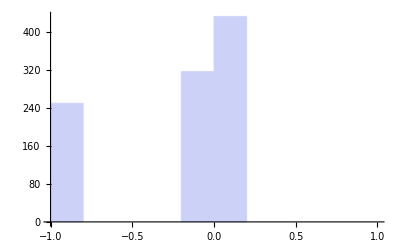

```mathematica
Histogram[vals,10]
```

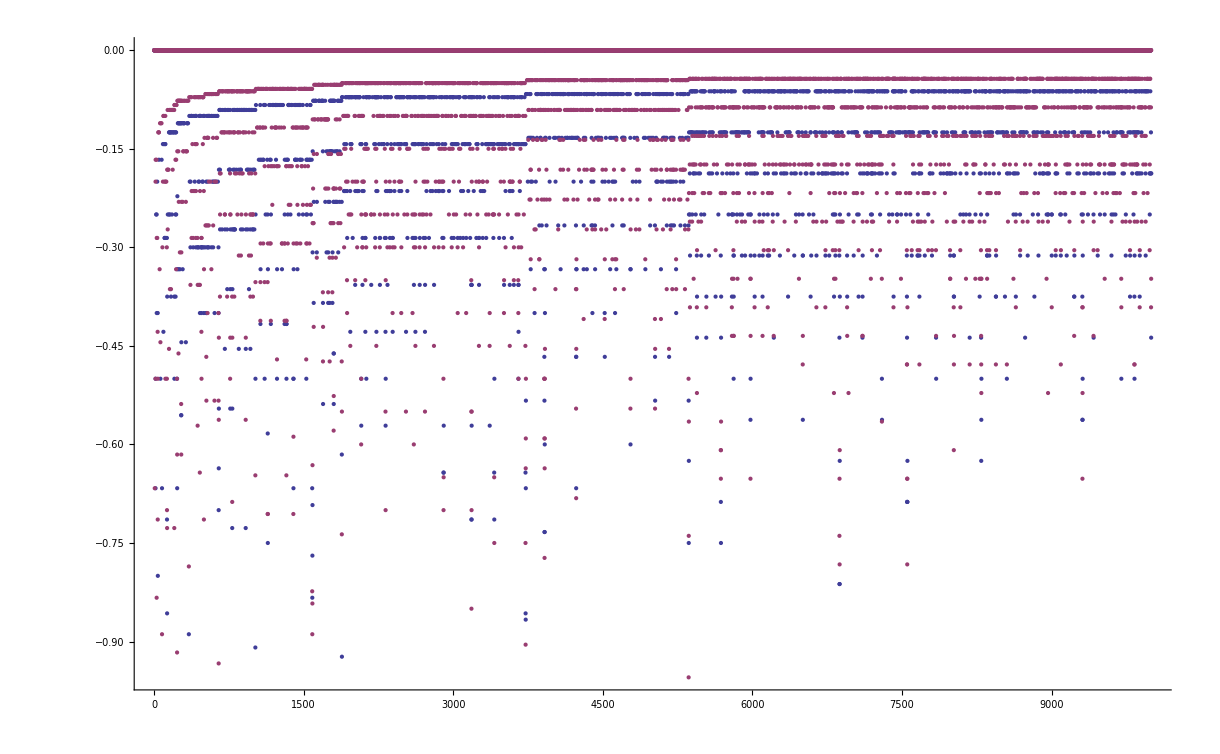

```mathematica
ListPlot[{vals2,vals3},PlotRange->All]
```

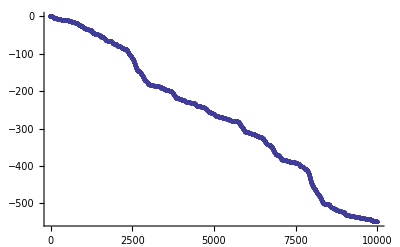

```mathematica
ListPlot[Accumulate[vals2]]
```

```mathematica
Skewness[vals2]
```

0.257406

```mathematica
vals2=CalcDeltas[{3,7},10^10000,10^20000,100000]
```

{0,-2/23,-9/23,-8/23,0,0,0,0,0,0,0,-2/23,0,0,0,-1/23,-3/23,-1/23,0,0,0,0,0,0,0,0,0,0,0,-6/23,0,0,0,-1/23,0,-1/23,0,0,0,-4/23,0,0,0,0,-2/23,0,0,0,-1/23,0,0,0,-1/23,-7/23,-21/23,-7/8,-21/25,-12/25,-12/25,-2/5,-7/25,0,0,0,-1/25,0,0,0,0,-4/25,-4/25,-3/25,0,0,0,0,0,0,0,0,0,-1/25,0,0,0,0,-1/5,0,0,0,-1/25,0,0,0,-1/25,0,0,0,0,-1/5,-7/25,-7/25,-4/25,0,0,0,0,0,0,-1/25,0,0,0,-1/25,-2/25,0,0,0,-1/25,0,-2/25,0,0,0,0,-3/25,0,0,0,0,0,0,0,0,0,0,0,0,0,-6/25,-9/25,-2/25,-2/25,0,0,0,0,0,0,0,-2/25,0,0,0,0,-3/25,-1/5,-3/25,-1/25,0,0,0,-1/25,0,0,«99671»,0,-1/30,0,0,0,-1/15,0,0,0,0,-1/15,-4/15,-1/6,-1/10,0,0,0,-1/30,0,0,0,-1/15,0,0,0,0,0,0,0,-2/15,-1/5,-7/30,-4/15,-1/15,0,0,0,-1/30,0,0,0,-2/15,-1/5,0,0,0,0,0,0,0,0,0,-1/30,0,0,0,0,-1/15,0,0,0,-1/30,-1/15,0,0,0,-1/30,0,0,0,0,-1/6,0,0,0,0,0,0,0,-1/15,0,0,0,0,0,0,-1/15,-1/30,-1/6,0,0,0,0,-1/30,0,0,0,0,0,0,0,-1/15,0,0,0,-1/30,0,-1/15,0,0,0,0,0,0,-1/30,-4/15,-4/15,-2/15,0,0,0,0,-1/30,0,0,0,0,0,0,0,-1/15,0,0,0,-1/30,0,-1/15,-1/30,0,0,0,-1/10,-1/15,0,0,0,0,-1/15,0,0,0,-1/5,-4/15,-1/15,0,0,0,-1/30,0,-1/10,-1/15,0,0,0}

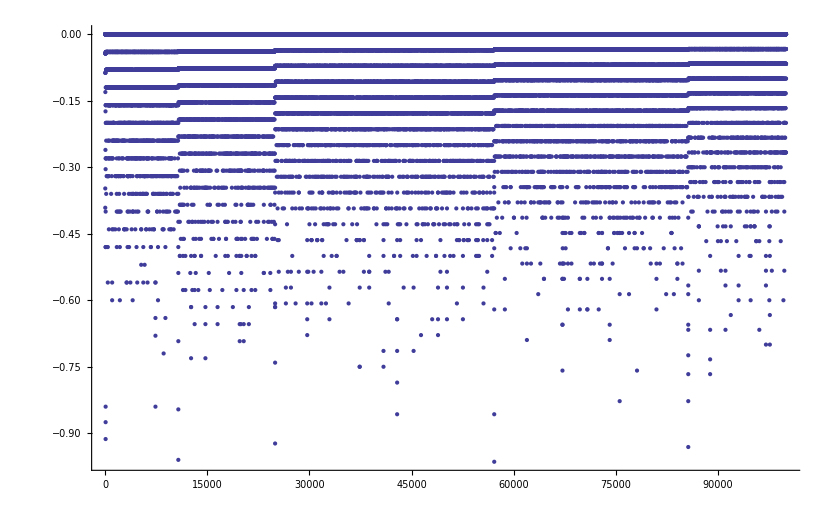

```mathematica
ListPlot[vals2,PlotRange->All]
```

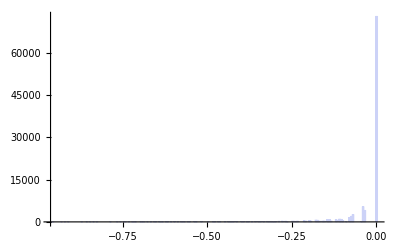

```mathematica
Histogram[vals2]
```

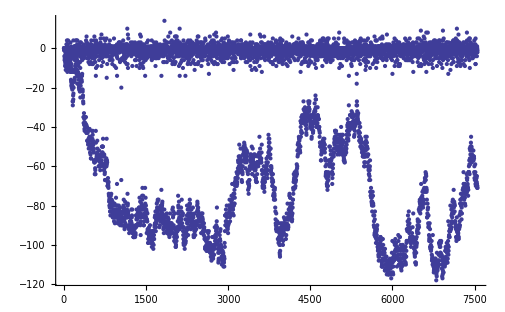

```mathematica
ListPlot[vals2]
```

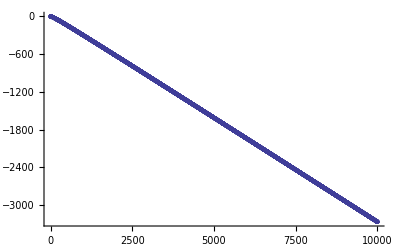

```mathematica
ListPlot[Accumulate[vals2]]
```

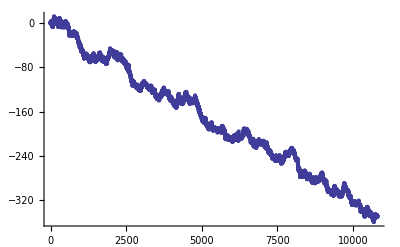

```mathematica
ListPlot[Accumulate[vals]]
```

```mathematica
Skewness[vals]
```

1.14538

```mathematica
Skewness[vals3]
```

1.68552

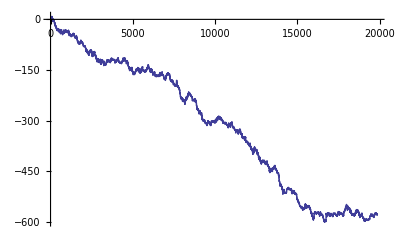

```mathematica
ListLinePlot[Accumulate[vals3]]
```

```mathematica
vals3=CalcDeltas[{3,5,7},0,10^100,10000]
```

Aborted at value : 283046454340137977956018378143784438094617010049587150179535111282289094555

{0.,0.,0.,0.63093,0.,-0.63093,0.,0.618684,0.,0.273914,0.,0.517462,0.,-1.03996,0.,1.89734,0.,2.85419,0.,-0.360321,0.,-1.23935,0.,-1.10293,0.,-0.688041,0.,-0.204343,0.,6.13236,0.,-0.0244346,0.,0.578759,0.,-0.208398,0.,0.635401,0.,-0.026203,0.,«19782»,0.686113,0.,-0.00206225,0.,0.262291,0.,0.29004,0.,-2.68453,0.,0.289295,0.,2.27855,0.,-2.16273,0.,0.211518,0.,0.337184,0.,-0.0829465,0.,0.212335,0.,-0.000113445,0.,-0.748494,0.,-0.0281333,0.,0.,0.,1.63093,0.,-0.63093,0.,0.,0.,0.,0.,0.}

```mathematica
Doebie[tuple_, start_,stopAt_] := Module[{current,lowest,logCurrent, index, dummy, range=1000, continue, distance,l=Length[tuple],zero=0,primeIndex=1, attempt=1, result={}},
index = 0;
current = start;
lowest = Infinity;
result={};

(* now calculate good values and append them to the file for as long as the bound is not reached *)
(* If the process is aborted, the file is closed *)

CheckAbort[
Monitor[
While[Length[result]<stopAt,
distance = Distance[current, tuple[[primeIndex]]];
logCurrent=N[Log[10,distance]];
If[logCurrent<lowest,lowest=Abs[logCurrent]];
current += distance;
If[tuple[[primeIndex]] ≠ tuple[[1]],
AppendTo[result , Take[IntegerDigits[current,tuple[[1]]],- FirstNonGood[tuple[[1]],current]]]
];
If [distance == 0,
zero+=1;
(*Print[{current,primeIndex,zero,distance}];*)
If[zero==l,
index +=1;
zero=0;
current+=1,
attempt=0,
lowest = Infinity
],
zero=0
];
attempt+=1;
primeIndex=Mod[primeIndex,l]+1;
]
,
"Calculating good values " <> ToString[tuple] <> ". " <> ToString[index] <> " found."<> "- " <> ToString[N[Log[10,current],50]] <> "  " <> ToString[Length[result]]<> "  " <> ToString[logCurrent]<> "  (" <> ToString[lowest] <> ")"
];
,
Print["Aborted at value : " <> ToString[current] ];
];
Return[result]
]
```

```mathematica
Doebie[{3,5,7,11},10^20,10]
```

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{1, 2, 0, 0, 2, 2, 1, 2, 2, 2, « 33 »}, -42/43].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{1, 2, 0, 2, 0, 2, 1, 1, 0, 1, « 33 »}, -42/43].

General::stop: Further output of Take will be suppressed during this calculation.

{Take[{1,2,0,0,2,2,1,2,2,2,1,1,0,2,1,0,0,0,2,1,2,2,1,2,1,0,1,1,2,2,0,0,1,0,2,0,1,2,1,2,0,0,2},-42/43],Take[{1,2,0,2,0,2,1,1,0,1,2,1,2,2,0,1,2,0,2,1,0,1,0,0,0,2,2,0,0,0,1,2,1,0,1,1,0,0,1,2,1,0,1},-42/43],Take[{1,2,0,2,0,2,1,1,0,1,2,1,2,2,0,2,1,0,2,0,0,0,0,2,0,2,2,1,2,2,2,0,2,2,0,0,2,0,0,0,2,2,1},-42/43],Take[{1,0,1,0,1,2,2,0,2,2,1,2,2,1,1,2,0,0,1,2,0,2,2,0,1,2,1,0,0,2,1,0,0,2,1,1,1,0,2,0,1,0,1,1},-39/44],Take[{1,0,1,1,1,1,1,2,2,1,0,2,0,2,1,1,0,1,1,1,2,0,2,0,0,1,2,1,0,0,1,0,1,2,0,2,2,0,1,0,1,2,0,2},-37/44],{1},Take[{1,0,0,0,0,0,0,0,1,0,2,2,0,2,0,0,2,0,1,2,0,2,2,2,0,0,2,2,1,1,1,2,2,0,2,1,0,2,0,0,0,1,2,0,1},-7/9],Take[{1,1,0,0,2,0,2,2,0,2,1,1,0,1,1,0,1,0,0,2,1,1,2,1,0,2,0,0,2,0,1,1,0,1,2,0,0,1,1,1,0,1,1,2,1},-41/45],Take[{1,1,0,0,2,2,0,0,0,1,0,0,0,2,2,0,0,0,0,0,1,1,0,1,0,1,1,0,1,2,2,0,0,0,1,1,0,0,1,1,2,1,2,2,2},-41/45],Take[{1,1,0,1,0,0,0,1,0,1,2,1,2,2,0,2,1,1,0,0,0,1,2,2,1,0,1,2,1,0,1,0,2,1,2,2,2,1,0,0,1,2,2,2,0},-7/9]}